```mathematica
(2 π)/(0.511*10^6)*1970
```

0.0242228

```mathematica
((4.136*10^-15)(3*10^8))/(0.6616*10^6)*10^10
```

0.0187545

```mathematica
e0=0.6616*10^6;
m=0.511*10^6;
energy[θ_,e0_]:=e0/(1+e0/m(1-Cos[θ]));
```

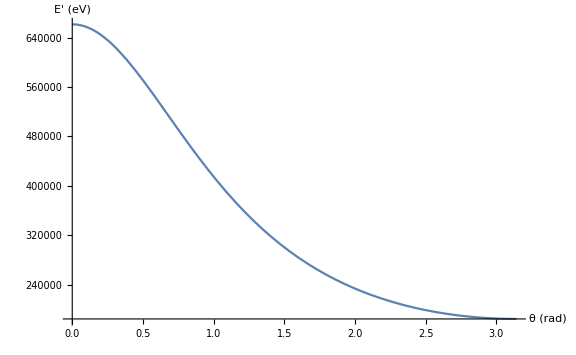

```mathematica
Plot[energy[θ,e0],{θ,0,π},AxesLabel->{"θ (rad)","E' (eV)"},ImageSize->Large]
```

```mathematica
energy[π,e0]
```

184319.

```mathematica
e0Na=0.511*10^6;
```

```mathematica
energy[π,e0Na]
```

170333.

```mathematica
Solve[{e0-energy[θ,e0]==%34},θ][[2]]//Quiet
```

{θ→0.749247}

```mathematica
(θ/.%40) * 180/π
```

42.9287

```mathematica
energy[θ/.%40,e0]
```

491267.

```mathematica
Sin[π/4]
```

1/(√2)

```mathematica
Sin[π/2]
```

1